```mathematica
Solve[1.13*^-18==(((6.626*^-34)/(2π))^2)/(2 0.043 9.11*^-31 Eg),Eg]
```

{{Eg→1.25617×10^-19}}

```mathematica
(1.2561683725873208*^-19)/(1.602*^-19)
```

0.784125

```mathematica
0.8161
```

```mathematica
x=.47;
.36+.505x+.555x^2
.324+.7x+.4x^2
.422+.7x+.4x^2
```

0.71995

0.74136

0.83936

```mathematica
Solve[ep==eq+(ℏ^2 k^2)/(2 mw(1+(2 mw γ)/ℏ^2(eq+ep))),ep]//Simplify
```

```mathematica
Clear[q,mw,me,γ,ℏ,eq]
Solve[ep==(ℏ^2 k^2)/(2 mw(1+(2 mw γ)/ℏ^2(eq+ep))),ep]//FullSimplify
```

{{ep→-(2 eq mw^2 γ+mw ℏ^2+√(mw^2 (4 k^2 γ ℏ^4+(2 eq mw γ+ℏ^2)^2)))/(4 mw^2 γ)},{ep→(-2 eq mw^2 γ-mw ℏ^2+√(mw^2 (4 k^2 γ ℏ^4+(2 eq mw γ+ℏ^2)^2)))/(4 mw^2 γ)}}

```mathematica
q=1.602*^-19;
mw=0.043 me;
me=9.11*^-31;
γ=1.13*^-18;
ℏ=1.055*^-34;
eq={0.0506,0.1975,0.3256}*q;
Es=eq/q+(-2 eq mw^2 γ-mw ℏ^2+√(mw^2 (4 k^2 γ ℏ^4+(2 eq mw γ+ℏ^2)^2)))/(q 4 mw^2 γ)//Simplify
```

{-0.367089+3.52543×10^67 √(1.40373×10^-136+5.59949×10^-154 k^2),-0.293639+3.52543×10^67 √(1.94082×10^-136+5.59949×10^-154 k^2),-0.229589+3.52543×10^67 √(2.48003×10^-136+5.59949×10^-154 k^2)}

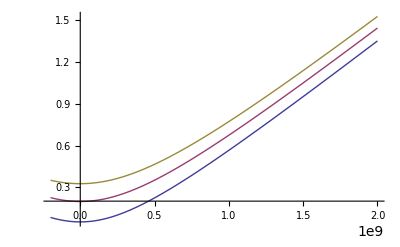

```mathematica
Plot[Es,{k,-2*^8,20*^8},PlotRange->All]
```

```mathematica
Es[[3]]/.k->0;
NSolve[%-0.034==Es[[2]],k]
```

{{k→-3.81497×10^8},{k→3.81497×10^8}}

```mathematica
Es[[2]]/.k->3.815*^8;
NSolve[%-0.034==Es[[2]],k]
```

{{k→-3.00033×10^8},{k→3.00033×10^8}}

```mathematica
3.8149686698764205*^8-3.000330156954258*^8
```

8.14639×10^7

```mathematica
Es[[2]]/.k->0;
NSolve[%-0.034==Es[[1]],k]
```

{{k→-3.92219×10^8},{k→3.92219×10^8}}

```mathematica
Es[[1]]/.k->3.922*^8;
NSolve[%-0.034==Es[[1]],k]
```

{{k→-3.21931×10^8},{k→3.21931×10^8}}

```mathematica
3.9221895812236786*^8-3.2193059688214576*^8
```

7.02884×10^7

```mathematica
((8.146385129221624*^7)/(7.02883612402221*^7))^2
```

1.34327

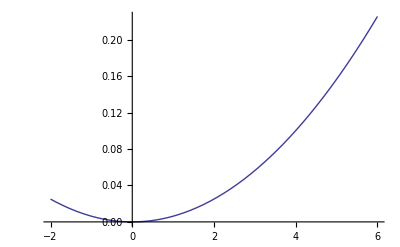

```mathematica
q=1.602*^-19;
mw=0.043 me;
me=9.11*^-31;
γ=1.13*^-18;
ℏ=1.055*^-34;
eq=0.3256q;
Plot[(ℏ^2 k^2)/(2 mw(1+(2 mw γ)/ℏ^2(eq))q),{k,-2*^8,6*^8}]
```